## Packages import and definitio ns

```mathematica
Get[NotebookDirectory[]<>"../QMB.wl"]
```

Es el segundo cuadero en el que uso esta definición, quizás vale la pena meterla en QMB.wl

```mathematica
ClearAll[ParityMatrix];ParityMatrix[L_]:=Normal@SparseArray[{FromDigits[#,2]+1,FromDigits[Reverse[#],2]+1}->1.&/@Tuples[{0,1},L]]
```

```mathematica
Parity[ψ_,L_]:=ψ[[FromDigits[Reverse[#],2]+1&/@Tuples[{0,1},L]]]
```

```mathematica
ClearAll[SFF]
SFF[eigenvals_,t_]:=Module[{spectrumSize},
spectrumSize=Length[eigenvals];
(1/spectrumSize^2)*
Chop[Total[Exp[I(eigenvals-RotateRight[eigenvals,#]&/@Range[0,spectrumSize-1])t],2]]
]
```

## Chaotic region (h_z=0.5, J=1)

```mathematica
L=11(*number of spins*);
{hx,hz,J}={1.,0.5,ConstantArray[1.,L-1]}
```

{1.,0.5,{1.,1.,1.,1.,1.,1.,1.,1.,1.,1.}}

```mathematica
Module[{H,eigenvecs},
H=IsingNNOpenHamiltonian[hx,hz,J,L];
{eigenvals,eigenvecs}=N[Chop[Transpose[Sort[Transpose[Eigensystem[H]]]]]];
evenEigenvals=eigenvals[[Flatten[Position[Round[ParallelMap[Braket[#,Parity[#,L]]&,eigenvecs],10.^0],1.]]]];
]
```

### Whole spectrum

```mathematica
(*time points*)
numberOftemporalPoints=500;
tValues=Range[0.01,0.09,0.01]~Join~Flatten[Table[10.^(-5x/#+i),{i,0,4},{x,#/5,1,-1}]]&[numberOftemporalPoints];
```

```mathematica
AbsoluteTiming[
sffData=ParallelTable[{t,SFF[eigenvals,t]},{t,tValues}];
]
```

{27.4257,Null}

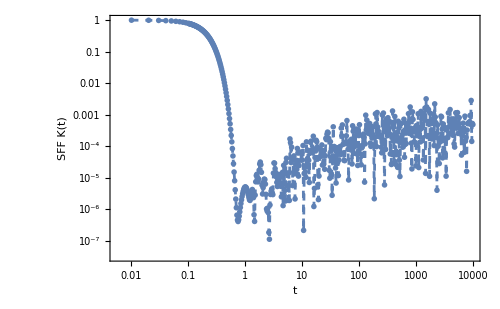

```mathematica
ListLogLogPlot[sffData,
Joined->True,
PlotStyle->Directive[Dashed],
PlotMarkers->{Automatic,Scaled[0.03]},
PlotRange->All,
Frame->True,
FrameStyle->Directive[Black,FontSize->20],
FrameLabel->{"StyleBox[\"t\",FontSlant->\"Italic\"]","SFF K(t)"},
GridLines->Automatic,
GridLinesStyle->Directive[Dashed,LightGray],
ImageSize->500]
```

### Even parity subspace

```mathematica
AbsoluteTiming[
sffData=ParallelTable[{t,SFF[evenEigenvals,t]},{t,tValues}];
]
```

{7.13458,Null}

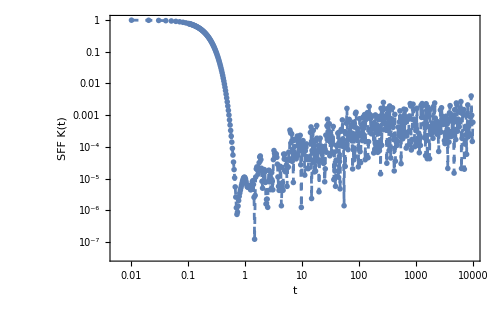

```mathematica
ListLogLogPlot[sffData,
Joined->True,
PlotStyle->Directive[Dashed],
PlotMarkers->{Automatic,Scaled[0.03]},
PlotRange->All,
Frame->True,
FrameStyle->Directive[Black,FontSize->20],
FrameLabel->{"StyleBox[\"t\",FontSlant->\"Italic\"]","SFF K(t)"},
GridLines->Automatic,
GridLinesStyle->Directive[Dashed,LightGray],
ImageSize->500]
```

## Regular region (h_z=2.5, J=1)

```mathematica
L=11(*number of spins*);
{hx,hz,J}={1.,2.5,ConstantArray[1.,L-1]}
```

{1.,2.5,{1.,1.,1.,1.,1.,1.,1.,1.,1.,1.}}

```mathematica
Module[{H,eigenvecs},
H=IsingNNOpenHamiltonian[hx,hz,J,L];
{eigenvals,eigenvecs}=N[Chop[Transpose[Sort[Transpose[Eigensystem[H]]]]]];
evenEigenvals=eigenvals[[Flatten[Position[Round[ParallelMap[Braket[#,Parity[#,L]]&,eigenvecs],10.^0],1.]]]];
]
```

### Whole spectrum

```mathematica
(*time points*)
numberOftemporalPoints=500;
tValues=Range[0.01,0.09,0.01]~Join~Flatten[Table[10.^(-5x/#+i),{i,0,4},{x,#/5,1,-1}]]&[numberOftemporalPoints];
```

```mathematica
AbsoluteTiming[
sffData=ParallelTable[{t,SFF[eigenvals,t]},{t,tValues}];
]
```

{29.1381,Null}

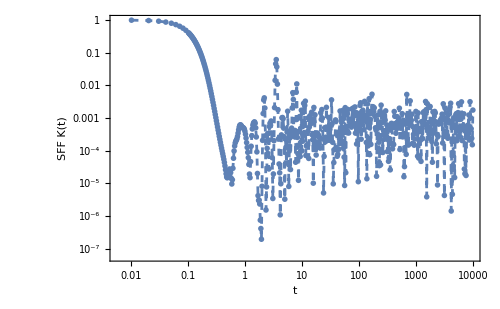

```mathematica
ListLogLogPlot[sffData,
Joined->True,
PlotStyle->Directive[Dashed],
PlotMarkers->{Automatic,Scaled[0.03]},
PlotRange->All,
Frame->True,
FrameStyle->Directive[Black,FontSize->20],
FrameLabel->{"StyleBox[\"t\",FontSlant->\"Italic\"]","SFF K(t)"},
GridLines->Automatic,
GridLinesStyle->Directive[Dashed,LightGray],
ImageSize->500]
```

### Even parity subspace

```mathematica
AbsoluteTiming[
sffData=ParallelTable[{t,SFF[evenEigenvals,t]},{t,tValues}];
]
```

{6.74945,Null}

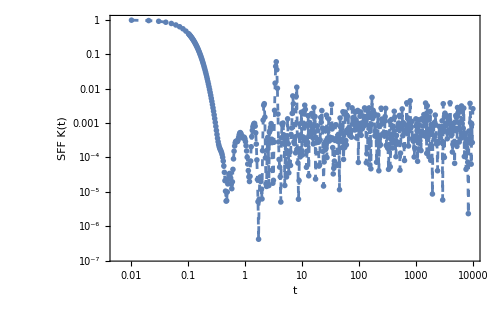

```mathematica
ListLogLogPlot[sffData,
Joined->True,
PlotStyle->Directive[Dashed],
PlotMarkers->{Automatic,Scaled[0.03]},
PlotRange->All,
Frame->True,
FrameStyle->Directive[Black,FontSize->20],
FrameLabel->{"StyleBox[\"t\",FontSlant->\"Italic\"]","SFF K(t)"},
GridLines->Automatic,
GridLinesStyle->Directive[Dashed,LightGray],
ImageSize->500]
```